120.634

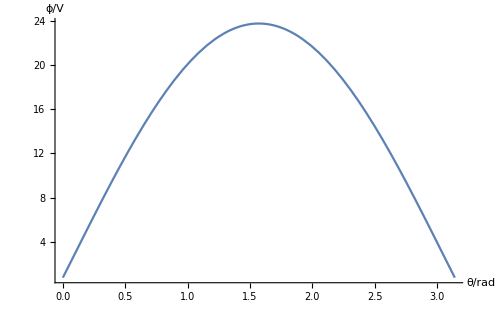

-Graphics3D-

```mathematica
a=120.6341826
Plot[(a*Sin[x])/(3*√3)+a/(2*√3*π)Sum[Exp[(-2*π)/3*√((l+m)^2+3*(l-m)^2)]/(√((l+m)^2+3*(l-m)^2))*(1-Exp[(-2*π)/3*Sin[x]*√((l+m)^2+3*(l-m)^2)]*Cos[(-2*π)/3*(2*l-m)*Cos[x]]),{l,-11,0},{m,-11,-1}]+a/(2*√3*π)Sum[Exp[(-2*π)/3*√((l+m)^2+3*(l-m)^2)]/(√((l+m)^2+3*(l-m)^2))*(1-Exp[(-2*π)/3*Sin[x]*√((l+m)^2+3*(l-m)^2)]*Cos[(-2*π)/3*(2*l-m)*Cos[x]]),{l,-11,0},{m,1,11}]+a/(2*√3*π)Sum[Exp[(-2*π)/3*√((l+m)^2+3*(l-m)^2)]/(√((l+m)^2+3*(l-m)^2))*(1-Exp[(-2*π)/3*Sin[x]*√((l+m)^2+3*(l-m)^2)]*Cos[(-2*π)/3*(2*l-m)*Cos[x]]),{l,1,11},{m,-11,0}]+a/(2*√3*π)Sum[Exp[(-2*π)/3*√((l+m)^2+3*(l-m)^2)]/(√((l+m)^2+3*(l-m)^2))*(1-Exp[(-2*π)/3*Sin[x]*√((l+m)^2+3*(l-m)^2)]*Cos[(-2*π)/3*(2*l-m)*Cos[x]]),{l,1,11},{m,0,11}],{x,0,π},AxesLabel->{"θ/rad","ϕ/V"},PlotRange->All]
Plot3D[(a*Sin[π/4])/(3*√3)+a/(2*√3*π)Sum[Exp[(-2*π)/3*√((l+m)^2+3*(l-m)^2)]/(√((l+m)^2+3*(l-m)^2))*(Cos[(2*π)/(3*1.5)*((l+m)*x+√3*(l-m)*y)]-Exp[(-2*π)/3*Sin[π/4]*√((l+m)^2+3*(l-m)^2)]*Cos[(2*π)/(3*1.5)*((l+m)*x+√3*(l-m)*y)-(2*π)/3*(2*l-m)*Cos[π/4]]),{l,-11,0},{m,-11,-1}]+a/(2*√3*π)Sum[Exp[(-2*π)/3*√((l+m)^2+3*(l-m)^2)]/(√((l+m)^2+3*(l-m)^2))*(Cos[(2*π)/(3*1.5)*((l+m)*x+√3*(l-m)*y)]-Exp[(-2*π)/3*Sin[π/4]*√((l+m)^2+3*(l-m)^2)]*Cos[(2*π)/(3*1.5)*((l+m)*x+√3*(l-m)*y)-(2*π)/3*(2*l-m)*Cos[π/4]]),{l,-11,0},{m,1,11}]+a/(2*√3*π)Sum[Exp[(-2*π)/3*√((l+m)^2+3*(l-m)^2)]/(√((l+m)^2+3*(l-m)^2))*(Cos[(2*π)/(3*1.5)*((l+m)*x+√3*(l-m)*y)]-Exp[(-2*π)/3*Sin[π/4]*√((l+m)^2+3*(l-m)^2)]*Cos[(2*π)/(3*1.5)*((l+m)*x+√3*(l-m)*y)-(2*π)/3*(2*l-m)*Cos[π/4]]),{l,1,11},{m,-11,0}]+a/(2*√3*π)Sum[Exp[(-2*π)/3*√((l+m)^2+3*(l-m)^2)]/(√((l+m)^2+3*(l-m)^2))*(Cos[(2*π)/(3*1.5)*((l+m)*x+√3*(l-m)*y)]-Exp[(-2*π)/3*Sin[π/4]*√((l+m)^2+3*(l-m)^2)]*Cos[(2*π)/(3*1.5)*((l+m)*x+√3*(l-m)*y)-(2*π)/3*(2*l-m)*Cos[π/4]]),{l,1,11},{m,0,11}],{x,-5,5},{y,-5,5},Mesh->None,ColorFunction->"Rainbow",PlotLegends->Automatic,AxesLabel->{"x/A","y/A","ϕ/V"},PlotRange->All]
```